# Projekt za Računalniška orodja v matematiki

23.3.2021

## Podatki, ki jih bomo uporabili

```mathematica
drzave=EntityList["Country"];
```

Povprečne mesečne, sezonske in pa letne temperature. (To bom dopolnil še kasneje.)

Uvozil bom podatke iz excela, ki povedo kolikšna je letna anomalija na svetovnem merilu glede na povprečje 20. stoletja, pridobljeni so pa na:

```mathematica
Hyperlink["https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021"]
```

https://www.ncdc.noaa.gov/cag/global/time-series/globe/land_ocean/ann/2/1880-2021

```mathematica
podatkiIzExcela = Import["C:\\Users\\ALEN\\Desktop\\FMF\\ROM\\Projekt_ROM_github\\data.csv", "CSV"];
```

```mathematica
podatkiIzExcelaVTabeli = podatkiIzExcela[[5;;,All ]] //TableForm;
```

```mathematica
seznamLet = Table[podatkiIzExcelaVTabeli[[1]][[i]][[1]],{i,2,Length[podatkiIzExcelaVTabeli[[1]]]}];
```

```mathematica
seznamAnomalijTemperatur=Table[podatkiIzExcelaVTabeli[[1]][[i]][[2]],{i,2,Length[podatkiIzExcelaVTabeli[[1]]]}];
```

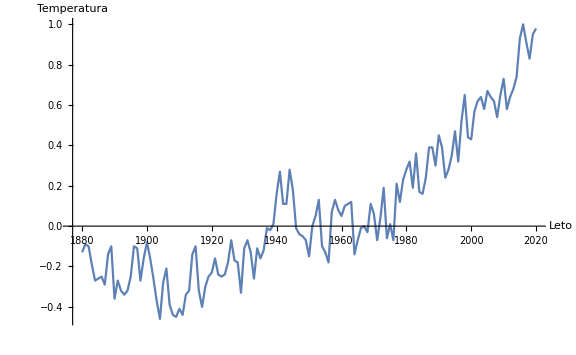

```mathematica
ListLinePlot[{seznamAnomalijTemperatur},DataRange->{1880, 2020},ImageSize->Large,AxesLabel->{"Leto","Temperatura"}]
```